h yn λ

h λ (yn+(h yn λ)/2)

h λ (yn+1/4 h yn λ (2+h λ))

h λ (yn+h λ (yn+1/4 h yn λ (2+h λ)))

1+z+z^2/2+z^3/6+z^4/24

{{0,0},{0,-2 √2},{0,2 √2},{Root-2.79Root[24+12 #1+4 #1^2+#1^3&,1]-2.785293563405282,0}}

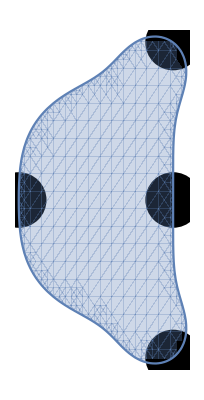

```mathematica
k1=h λ yn
k2 = h λ(yn + 1/2 k1)//FullSimplify
k3=h λ(yn + 1/2 k2)//FullSimplify
k4 = h λ(yn + k3)//FullSimplify
f[z_]=((yn+1/6(k1+2k2+2k3+k4))/yn)/.h->z/λ//Expand
vals=ReIm[Assuming[Re[z]==0∨Im[z]==0,SolveValues[Abs[f[z]]==1,z]]]
Show[Graphics[{PointSize[.1],Point[vals]}],ComplexRegionPlot[Abs[f[z]]<1,{z,-3(1+ⅈ),3(1/3+ⅈ)}]]
```

```mathematica
Manipulate[ContourPlot[ComplexExpand[Abs[f[x+ⅈ y]]^2]==ϵ,{x,-3,0.5},{y,-3,3}],{ϵ,0,1}]
```